## Init

```mathematica
(*rotation*)
R={{1/(√2),0,0,0,0,1/(√2),0,0},{0,1/(√2),0,0,0,0,1/(√2),0},{0,0,1/2,0,0,0,0,(√3)/2},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{-1/(√2),0,0,0,0,1/(√2),0,0},{0,-1/(√2),0,0,0,0,1/(√2),0},{0,0,(-√3)/2,0,0,0,0,1/2}};
```

```mathematica
(*Definition of the f-tensor*)
f[i_,j_,k_]:=0;

f[1,2,3]=f[2,3,1]=f[3,1,2]=1;
 
f[1,3,2]=f[2,1,3]=f[3,2,1]=-1;

f[1,4,7]= f[4,7,1]=f[7,1,4]=
f[1,6,5]=f[6,5,1]=f[5,1,6]=
 f[2,4,6]= f[4,6,2]= f[6,2,4]=
f[2,5,7]=f[5,7,2]=f[7,2,5]=
 f[3,4,5]= f[4,5,3]= f[5,3,4]=
 f[3,7,6]=  f[7,6,3]= f[6,3,7]=1/2;

f[1,7,4]=f[7,4,1]=f[4,1,7]=
f[1,5,6]=f[5,6,1]=f[6,1,5]=
 f[2,6,4]= f[6,4,2]= f[4,2,6]=
f[2,7,5]=f[7,5,2]=f[5,2,7]=
 f[3,5,4]= f[5,4,3]= f[4,3,5]=
 f[3,6,7]= f[6,7,3]= f[7,3,6]=-1/2;


f[4,5,8]=f[5,8,4]=f[8,4,5]=
 f[6,7,8]= f[7,8,6]= f[8,6,7]=√3/2; 

f[4,8,5]=f[8,5,4]=f[5,4,8]=
 f[6,8,7]= f[8,7,6]= f[7,6,8]=-√3/2; 

(*Definition of the d-tensor*)

d[i_,j_,k_]=0;
d[1,1,8]=d[1,8,1]=d[8,1,1]=
d[2,2,8]=d[2,8,2]=d[8,2,2]=
d[3,3,8]=d[3,8,3]=d[8,3,3]=1/(√3);
d[8,8,8]=-1/(√3);
d[1,4,6]=d[1,6,4]=d[4,1,6]=d[4,6,1]=d[6,1,4]=d[6,4,1]=
d[1,5,7]=d[1,7,5]=d[5,1,7]=d[5,7,1]=d[7,1,5]=d[7,5,1]=
d[2,5,6]=d[2,6,5]=d[5,2,6]=d[5,6,2]=d[6,2,5]=d[6,5,2]=
d[3,4,4]=d[4,3,4]=d[4,4,3]=
d[3,5,5]=d[5,3,5]=d[5,5,3]=1/2;
d[2,4,7]=d[2,7,4]=d[4,2,7]=d[4,7,2]=d[7,2,4]=d[7,4,2]=
d[3,6,6]=d[6,3,6]=d[6,6,3]=
d[3,7,7]=d[7,3,7]=d[7,7,3]=-1/2;
d[4,4,8]=d[4,8,4]=d[8,4,4]=
d[5,5,8]=d[5,8,5]=d[8,5,5]=
d[6,6,8]=d[6,8,6]=d[8,6,6]=
d[7,7,8]=d[7,8,7]=d[8,7,7]=-1/(2 √3);
```

## Constants

```mathematica
Sites=6;
```

```mathematica
tmax=20;
```

```mathematica
Nt=128;
dt=tmax/Nt;
Length[ts=N@Range[0,tmax-dt,dt]];
```

```mathematica
times=Table[t,{t,0,tmax-dt,dt}];
```

```mathematica
Runs=1000;
mSIM=10;
```

```mathematica
Uvalue=1;
μvalue=1;
Jvalue=0.01;
navgvalue=1;
```

```mathematica
putvalues:={U->Uvalue,J->Jvalue,navg->navgvalue,μ->μvalue};
```

## Get QM

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/siteone";
```

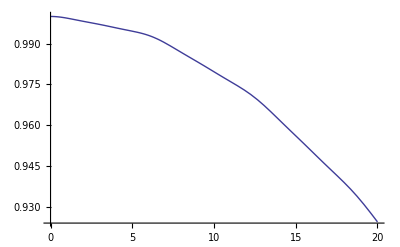

```mathematica
QMS1=%;
```

## Get Wig SU3

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/ht";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/su3dw6uj10010t";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/su3dw6uj100ht";
```

```mathematica
avgspins3=%;
```

```mathematica
Dimensions[avgspins]
```

{128,6,8}

```mathematica
TWAsu3=ListPlot[{{times,2avgspins3[[All,1,3]]}ᵀ,{times,2avgspins3[[All,4,3]]}ᵀ},Joined->True,PlotStyle->Dotted];
```

## Get Wig SU2

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/su2dw6ht";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/sofarsu2";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/su2dw6uj1001m";
```

```mathematica
avgspins2=%;
```

```mathematica
Dimensions[avgspins2]
```

{128,6,3}

```mathematica
TWAsu2=ListPlot[{{times,avgspins2[[All,1,3]]}ᵀ,{times,avgspins2[[All,4,3]]}ᵀ},Joined->True,PlotStyle->Dashed];
```

## Plots

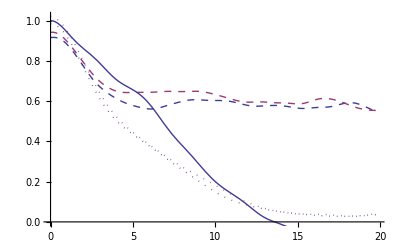

```mathematica
Show[TWA6,TWAsu2,szplus6]
```

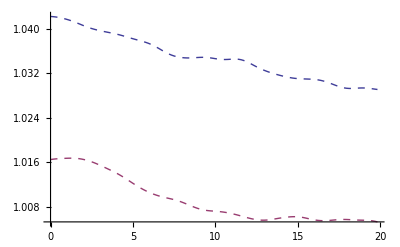

```mathematica
Show[TWAsu2]
```

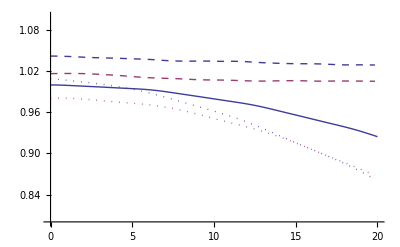

```mathematica
Show[TWAsu2,TWAsu3,QMS1,PlotRange->{0.8,1.1},AxesOrigin->{0,0.8}]
```